Metoda půlení intervalu pro hledání kořenu nelineární rovnice

nechť je kořen ohraničen [a_0, b_0] tak, že platí f(a_0)*f(b_0) < 0

vypočítáme x_1 = (a_0+ b_0)/2

jeden krajní bod ponecháme, druhý posuneme do x_1, aby opět platilo f(a_1)*f(b_1) < 0

po n-tém kroku je kořen omezený intervalem [a_n, b_n]

nepřesnost kořene ϵ  = |a_n - b_n|

spolehlivá metoda

blízko kořene pomalá

úkol 1.  Najděte kořen rovnice f(x) = sin(x) - 0.5 metodou půlení intervalu.

```mathematica
f[x_]:=Sin[x]-.5  (*definice f(x)*)
a=0; (*volba počátečního intervalu*)
b=1;
reseni={};
chyba={};
iterace= 50; (*celkový počet iterací*)
```

```mathematica
For[i=1,i<iterace,i++,
c=(a+b)/2;
AppendTo[reseni,c];
AppendTo[chyba,Abs[a-b]];
If[
f[a]*f[c]<0,
b=c,
a=c
]
]
```

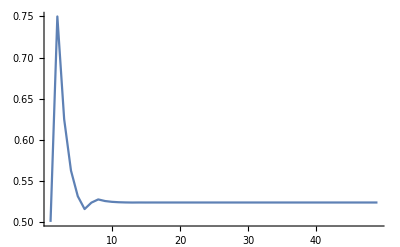

```mathematica
ListLinePlot[reseni,PlotRange->All]
```

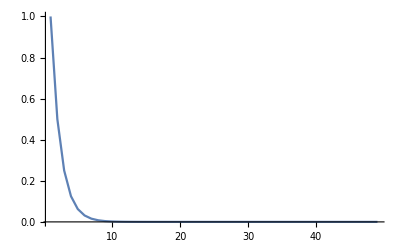

```mathematica
ListLinePlot[chyba,PlotRange->All]
```

Metoda sečen pro hledání kořenu nelineární rovnice

mějme body a_n, a_(n-1)

zvolme a_(n+1) v průsečíku spojnice bodů {a_(n-1) , f(a_(n-1) )} a {a_n , f(a_n )} s osou x

konvergence není zaručena

úkol 2.  Najděte kořen rovnice f(x) = exp(x) - 6 metodou půlení intervalu.

```mathematica
g[x_]:=Exp[x]-6
iteraci=15;
xi=0;
xip1=5;
res={};
chyb={};
aa=xip1;
```

```mathematica
For[i=1,i≤iteraci,i++,
cc=N[(xi*g[xip1]-g[xi]*xip1)/(g[xip1]-g[xi])];
xi=xip1;
xip1=cc;
AppendTo[res,cc];
AppendTo[chyb,Abs[xi-xip1]];
]
```

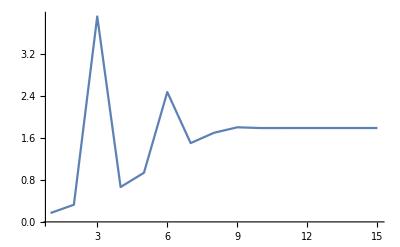

```mathematica
ListLinePlot[res,PlotRange->All]
```

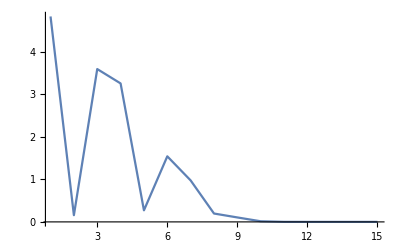

```mathematica
ListLinePlot[chyb,PlotRange->All]
```

Metoda Regula Falsi (tětiva)pro hledání kořenu nelineární rovnice

vylepšená metoda sečen

po určení a_(n+1) se k němu vybere z a_(n-1) a a_n takový bod OverBar[a_n], aby kořen zůstal ohraničený, tj.  f(a_(n+1) )*f(OverBar[a_n],) < 0

konvergence je zaručena

Newton-Raphsonova (tečnová) metoda

využívá první derivaci zadané funkce (je vhodná, pokud umíme hodnoty derivací rychle počítat)

Taylorův rozvoj zadané funkce v okolí bodu x_i: f(x_i+δ) = f(x_i) + δf'(x_i) + δ^2f''(x_i)/2 + ...

vypočítáme δ z podmínky f(x) = 0

iterační předpis: x_(i+1)= x_i- f(x_i)/f'(x_i)

konvergence není zaručena

úkol 3.  Najděte kořen rovnice f(x) = exp(x) - 6 tečnovou metodou.

```mathematica
dg[x_]:=Exp[x]
```

```mathematica
iter=10;
xi=0;
xip1=5;
rese={};
chyby={};
```

```mathematica
For[i=1,i≤iter,i++,
c=N[xip1-g[xip1]/dg[xip1]];
AppendTo[chyby,Abs[xi-xip1]];
xi=xip1;
xip1=c;
AppendTo[rese,c]
]
```

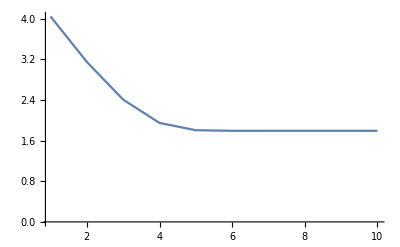

```mathematica
ListLinePlot[rese,PlotRange->All]
```

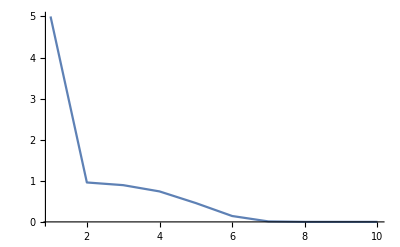

```mathematica
ListLinePlot[chyby,PlotRange->All]
```

Mullerova metoda

odvození http://kfe.fjfi.cvut.cz/~vachal/edu/nme/cviceni/05_nelin/DOCS/teorie_Mullerova_metoda.pdf

úkol 4.  Najděte kořen rovnice f(x) = 4x^3 - 2x^2 - 4x - 3 Muellerovou metodou.

```mathematica
(*chceme nalézt kořen polynomu P(x)*)
```

```mathematica
h[x_]:=4x^3-2x^2-4x-3
```

```mathematica
presnost=10^(-6);(*požadovaná přesnost*)
n=1; (*č. iterace*)
(*známe 3 body a odpovídající funkční hodnoty*)
x1=-10.;
x2=3.;
x3=0; (*volba nejblíž kořenu*)
y1=h[x1];
y2=h[x2];
y3=h[x3];
```

```mathematica
bodyx={};
```

```mathematica
(*hodnoty y1,y2,y3 proložíme Lagrangeovým interpolačním polynomem*)
```

```mathematica
While[Abs[y3]>presnost,
a1=y1/((x1-x2)*(x1-x3));
a2=y2/((x2-x1)*(x2-x3));
a3=y3/((x3-x1)*(x3-x2));
A=a1+a2+a3;
CC=x2*x3*a1+x1*x3*a2+x1*x2*a3;
B=-(x2+x3)*a1-(x1+x3)*a2-(x1+x2)*a3;
xn=(-B+Sqrt[B*B-4*A*CC])/(2*A);
xn0=(-B-Sqrt[B*B-4*A*CC])/(2*A);
If[Abs[xn0-x3]<Abs[xn-x3],xn=xn0
];
x1=x2;
x2=x3;
x3=xn;
AppendTo[bodyx,{x1,x2,x3}];
y1=y2;
y2=y3;
y3=h[xn];
n=n+1;
]
```

```mathematica
n
```

8

```mathematica
xn
```

-0.5-0.5 ⅈ

```mathematica
Solve[h[x]==0,x]
```

{{x→-1/2-ⅈ/2},{x→-1/2+ⅈ/2},{x→3/2}}

```mathematica
bodyx
```

{{2.,1.1,1.47737},{1.1,1.47737,1.49898},{1.47737,1.49898,1.5},{1.49898,1.5,1.5}}

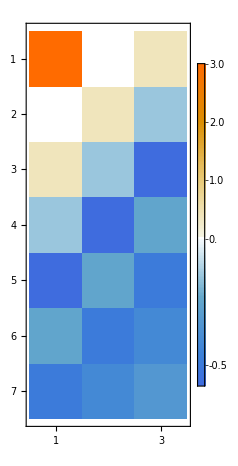

```mathematica
MatrixPlot[bodyx,PlotLegends->Automatic]
```

```mathematica
Dimensions[bodyx]
```

{4,3}

```mathematica
data={{bodyx[[1,1]],h[bodyx[[1,1]]]},{bodyx[[1,2]],h[bodyx[[1,2]]]},{bodyx[[1,3]],h[bodyx[[1,3]]]}};
```

```mathematica
nl=NonlinearModelFit[data,aá*x^2+bb*x+ce,{aá,bb,ce},x]
```

FittedModel[10.0008-31.1194 x+16.3095 x^2]

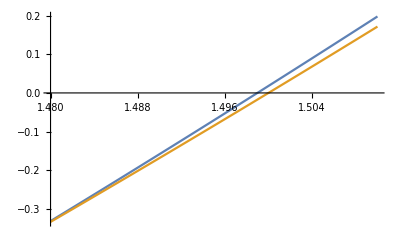

```mathematica
Plot[{nl[x],h[x]},{x,1.48,1.51}]
```

Soustavy nelineárních rovnic

řešíme soustavu f⃗(x⃗)=OverVector[0]

přepíšeme ji do tvaru
f_1(x_1,x_2,... ,x_n)=0
f_2(x_1,x_2,... ,x_n)=0
	...
f_n(x_1,x_2,... ,x_n)=0

metoda prosté iterace

soustavu lze přepsat do tvaru x⃗=ϕ⃗(x⃗)

x_1=ϕ_1(x⃗)
x_2=ϕ_2(x⃗)
     ...
x_n=ϕ_n(x⃗)

soustava má stejné řešení, jako původní soustava

iterační předpis (x⃗)_(k+1)=ϕ⃗((x⃗)_k)

úkol 1. řešte následující soustavu rovnic metodou prosté iterace

```mathematica
f1[x_,y_]:=x^2+4x-y^2-2y-1
f2[x_,y_]:=x^2+5y-4 (*původní rovnice f1,f2*)
ϕ1[x_,y_]:=(y^2+2y+1-x^2)/4
ϕ2[x_,y_]:=(4-x^2)/5 (*z nich parametrické vyjádření x=phi1, y=phi2*)
```

```mathematica
Solve[{f1[x,y],f2[x,y]}=={0,0},{x,y}]
```

{{x→Root0.637Root[81-100 #1-43 #1^2+#1^4&,1]0.6371078452969544,y→1/5 (4-(Root0.637Root[81-100 #1-43 #1^2+#1^4&,1]0.6371078452969544)^2)},{x→Root7.42Root[81-100 #1-43 #1^2+#1^4&,2]7.41689185374279,y→1/5 (4-(Root7.42Root[81-100 #1-43 #1^2+#1^4&,2]7.41689185374279)^2)},{x→Root-4.03-0.962 ⅈRoot[81-100 #1-43 #1^2+#1^4&,3]-4.026999849519872,y→1/5 (4-(Root-4.03-0.962 ⅈRoot[81-100 #1-43 #1^2+#1^4&,3]-4.026999849519872)^2)},{x→Root-4.03+0.962 ⅈRoot[81-100 #1-43 #1^2+#1^4&,4]-4.026999849519872,y→1/5 (4-(Root-4.03+0.962 ⅈRoot[81-100 #1-43 #1^2+#1^4&,4]-4.026999849519872)^2)}}

```mathematica
N[%68]
```

{{x→0.637108,y→0.718819},{x→7.41689,y→-10.2021},{x→-4.027-0.961677 ⅈ,y→-2.25838-1.54907 ⅈ},{x→-4.027+0.961677 ⅈ,y→-2.25838+1.54907 ⅈ}}

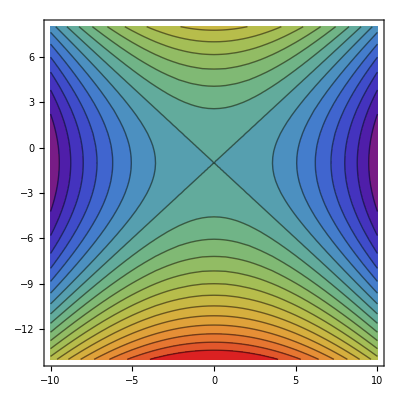

```mathematica
ContourPlot[ϕ1[x,y],{x,-10,10},{y,-14,8},ColorFunction->"Rainbow",Contours->20]
```

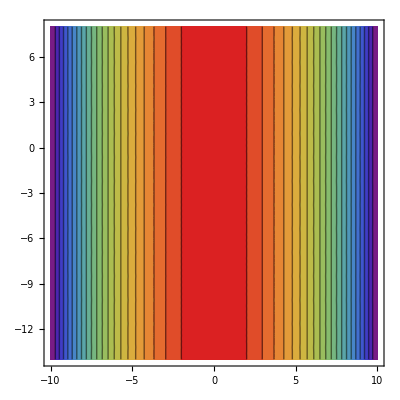

```mathematica
ContourPlot[ϕ2[x,y],{x,-10,10},{y,-14,8},ColorFunction->"Rainbow",Contours->20]
```

```mathematica
Plot3D[{f1[x,y],f2[x,y],0},{x,-10,10},{y,-14,8}]
```

-Graphics3D-

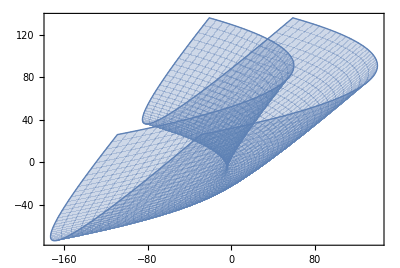

```mathematica
ParametricPlot[{f1[x,y],f2[x,y]},{x,-10,10},{y,-14,8}]
```

```mathematica
n=20; (*pocet kroku*)
x0=0.; (* pocatecni odhad x*)
y0=0.;(* pocatecni odhad y*)
```

```mathematica
For[i=1,i≤n,i++,
Print[{x0,y0}];
xn=ϕ1[x0,y0];
yn=ϕ2[x0,y0];
x0=xn;
y0=yn;
]
```

{0.,0.}

{0.25,0.8}

{0.794375,0.7875}

{0.641031,0.673794}

{0.597666,0.717816}

{0.648422,0.728559}

{0.641866,0.71591}

{0.633089,0.717601}

{0.637338,0.71984}

{0.637912,0.71876}

{0.636801,0.718614}

{0.637029,0.718897}

{0.6372,0.718839}

{0.637096,0.718795}

{0.637092,0.718822}

{0.637116,0.718823}

{0.637109,0.718817}

{0.637106,0.718818}

{0.637108,0.718819}

{0.637108,0.718819}

Newton - Raphsonova metoda

přesné řešení ξ⃗ vyjádříme ve tvaru ξ⃗=x⃗+δ x⃗

hodnotu funkce v bodě ξ⃗ vyjádříme pomocí Taylorova rozvoje 
f_i(x⃗+δ x⃗)=f_i(x⃗)+∑_(j=1)^n (∂f_i)/(∂x_j)δx_j+O(δ(x⃗)^2)

zanedbáním O(δ(x⃗)^2) získáme:
f_i(x⃗+δ x⃗)=f_i(x⃗)+∑_(j=1)^n (∂f_i)/(∂x_j)δx_j=0

řešíme tedy soustavu n lineárních rovnic s neznámou δ x⃗

iterační vztah: ((x⃗)_i)^(k+1)=((x⃗)_i)^k+δx_i^k

úkol 2. Pomocí Newton-Raphsonovy metody najděte řešení soustavy nelineárních rovnic

```mathematica
Clear[{f1,f2}]
```

Clear::ssym: {f1,f2} is not a symbol or a string.

```mathematica
stupen=2;
h=0.01; (*délka kroku*)
dfdx[f_,x_,y_,h_]:=1/(2h)*(f[x+h,y]-f[x-h,y])
```

```mathematica
dfdy[f_,x_,y_,h_]:=1/(2h)*(f[x,y+h]-f[x,y-h])
```

```mathematica
f1
```

f1

```mathematica
f1[x,y]
```

-1+4 x+x^2-2 y-y^2

```mathematica
f2[x,y]
```

-4+x^2+5 y

```mathematica
dfdx[f1,x,y,h]
```

50. (-4 (-0.01+x)-(-0.01+x)^2+4 (0.01+x)+(0.01+x)^2)

```mathematica
A
```

{{0.,0.},{0.,0.}}

```mathematica
b
```

{{1.},{1.}}

```mathematica
A[[1,1]]
```

0.

```mathematica
dfdx[f1,x0,y0,h]
```

6.

```mathematica
LinearSolve[A,b]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{0.,0.},{0.,0.}},{{1.},{1.}}]

```mathematica
A[[1,1]]=dfdx[f1,x0,y0,h];
A[[1,2]]=dfdy[f1,x0,y0,h];
A[[2,1]]=dfdx[f2,x0,y0,h];
A[[2,2]]=dfdy[f2,x0,y0,h];
b[[1,1]]=-f1[x0,y0];
b[[2,1]]=-f2[x0,y0];
```

```mathematica
A
```

{{6.,-4.},{2.,5.}}

```mathematica
b
```

{{-1.},{-2.}}

```mathematica
dx=LinearSolve[A,b];
```

```mathematica
dx
```

{{-0.342105},{-0.263158}}

```mathematica
n=20;
x0=1.;
y0=1.;
A={{0.,0.},{0.,0.}};
b={{1.},{1.}};
```

```mathematica
For[i=1,i≤n,i++,
A[[1,1]]=dfdx[f1,x0,y0,h];
A[[1,2]]=dfdy[f1,x0,y0,h];
A[[2,1]]=dfdx[f2,x0,y0,h];
A[[2,2]]=dfdy[f2,x0,y0,h];
b[[1,1]]=-f1[x0,y0];
b[[2,1]]=-f2[x0,y0];
dx=LinearSolve[A,b];
x0=x0+dx[[1,1]];
y0=y0+dx[[2,1]];
]
```

```mathematica
A
```

```mathematica
x0
```

0.637108

```mathematica
y0
```

0.718819